2.

0.2

0.01

0.04

Metric ready for R0 = 2 m

Asymptotic g_tt as l → +∞: -1.

Asymptotic g_tt as l → -∞: -1.

Φ(0)   = 0.

Φ'(0)  = 0.

Φ''(0) = -0.0025

NEC at throat (l = 0): -0.0200933

Sample values of l(s):

{{0,{-10.}},{40,{30.}},{80,{70.}},{120,{110.}},{160,{150.}},{200,{190.}}}

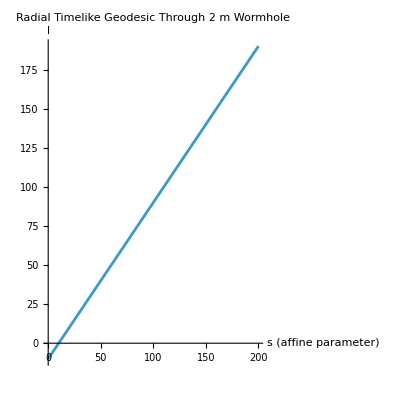

```mathematica
(* ::Title::*)(*Two-Sided Wormhole:NEC at Throat+Geodesic Across Universes*)ClearAll["Global`*"];

(*===========================================================*)
(*Parameters scaled for a 2 meter radial throat*)
(*===========================================================*)

R0=2.0
w=0.2
A=0.01
ε=0.04

(*Proper radial coordinate*)
r[l_]:=Sqrt[l^2+R0^2];

(*Shape function (same formula,different scale)*)
ϕ[l_]:=-A (1-R0/r[l]) Exp[-(r[l]-R0)^2/w^2];

(*===========================================================*)
(*Metric in (t,l,θ,φ) coordinates*)
(*===========================================================*)

coords={t,l,th,ph};

metric=DiagonalMatrix[{-Exp[2 ϕ[l]],Exp[-2 ϕ[l]],Exp[-2 ϕ[l]] r[l]^2,Exp[-2 ϕ[l]] r[l]^2 Sin[th]^2}];

Print["Metric ready for R0 = 2 m"];

(*===========================================================*)
(*Check asymptotic flatness*)
(*===========================================================*)

limitp=Limit[metric[[1,1]],l->Infinity];
limitm=Limit[metric[[1,1]],l->-Infinity];

Print["Asymptotic g_tt as l → +∞: ",limitp//N];
Print["Asymptotic g_tt as l → -∞: ",limitm//N];

(*===========================================================*)
(*NEC at the throat (l=0)*)
(*===========================================================*)

Phi0=ϕ[0];
Phi1=D[ϕ[l],l]/. l->0;
Phi2=D[ϕ[l],{l,2}]/. l->0;

NECThroat=((-Phi1^2 R0^2+Phi2 R0^2-1) Exp[4 Phi0])/(4 Pi R0^2)//N;

Print["Φ(0)   = ",Phi0//N];
Print["Φ'(0)  = ",Phi1//N];
Print["Φ''(0) = ",Phi2//N];
Print["NEC at throat (l = 0): ",NECThroat];

(*===========================================================*)
(*Radial timelike geodesic across throat*)
(*===========================================================*)

Clear[s,ell,τ];

Lgeo=-Exp[2 ϕ[ell[s]]] τ'[s]^2+Exp[-2 ϕ[ell[s]]] ell'[s]^2;

eqTau=D[D[Lgeo,τ'[s]],s]-D[Lgeo,τ[s]]==0;
eqEll=D[D[Lgeo,ell'[s]],s]-D[Lgeo,ell[s]]==0;

(*Start 5 throat radii on left side:l=-10 m*)
geoIC={τ[0]==0,ell[0]==-5 R0,(*Start at l=-10 m*)τ'[0]==1,ell'[0]==1};

geoSol=NDSolve[{eqTau,eqEll}~Join~geoIC,{τ,ell},{s,0,200},(*must increase domain because distances are larger*)MaxStepFraction->1/200];

Print["Sample values of l(s):"];
Print[Table[{ss,ell[ss]/. geoSol},{ss,0,200,40}]];

ParametricPlot[Evaluate[{s,ell[s]}/. geoSol],{s,0,200},AxesLabel->{"s (affine parameter)","l"},PlotRange->All,PlotLabel->"Radial Timelike Geodesic Through 2 m Wormhole"]
```